```mathematica
Population[r_]:=
(
x=Table[n,{n,1,200}];
 x[[1]]=0.5;
For[n=2,n≤200,n++,x[[n]]=r*x[[n-1]]*(1-x[[n-1]])];
ListPlot[x]
)
```

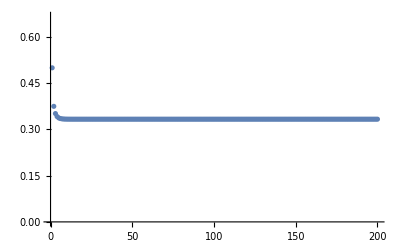

```mathematica
Population[1.5]
```

```mathematica
LegendreP[1,0]
```

0

```mathematica
LegendreP[1,1]
```

1

```mathematica
LegendreP[2,1]
```

1